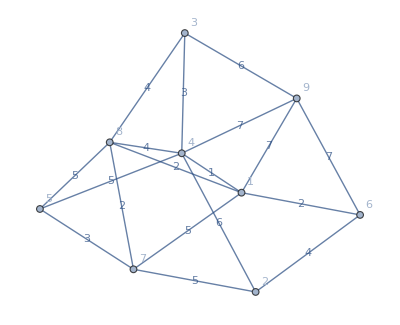

```mathematica
graph=RandomWeightedGraph[{9,18},RandomInteger[{1,7}]&,VertexLabels->Automatic,EdgeLabels->"EdgeWeight"]
```

```mathematica
weight=AnnotationValue[graph,EdgeWeight]
```

{1,2,5,2,7,6,4,5,3,4,6,5,4,7,3,5,7,2}

```mathematica
costvector=SymbolicIndexedArray[c,EdgeCount[graph]]
```

{c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13,c14,c15,c16,c17,c18}

```mathematica
decisionvector=SymbolicIndexedArray[x,EdgeCount[graph]]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18}

```mathematica
costvector.decisionvector
```

c1 x1+c2 x2+c3 x3+c4 x4+c5 x5+c6 x6+c7 x7+c8 x8+c9 x9+c10 x10+c11 x11+c12 x12+c13 x13+c14 x14+c15 x15+c16 x16+c17 x17+c18 x18

```mathematica
IncidenceMatrix[graph]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0)

```mathematica
IncidenceMatrix[graph][[{1,2,3}]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
LinearOptimization[weight.decisionvector,]
```

```mathematica
OddNodes[graph]
```

{1,2,3,5,6,8}

```mathematica
Subsets[OddNodes[graph],{1,17,2}]
```

{{1},{2},{3},{5},{6},{8},{1,2,3},{1,2,5},{1,2,6},{1,2,8},{1,3,5},{1,3,6},{1,3,8},{1,5,6},{1,5,8},{1,6,8},{2,3,5},{2,3,6},{2,3,8},{2,5,6},{2,5,8},{2,6,8},{3,5,6},{3,5,8},{3,6,8},{5,6,8},{1,2,3,5,6},{1,2,3,5,8},{1,2,3,6,8},{1,2,5,6,8},{1,3,5,6,8},{2,3,5,6,8}}

```mathematica
MemberQ[{1,2,3},1]
```

True

```mathematica
MemberQ[{1,2,3},2]
```

True

```mathematica
FreeQ[{1,2,3},2]
```

False

```mathematica
{{-Graphics-, CodeEquivalentQ}}[!MemberQ[{1,2,3},1],FreeQ[{1,2,3},1]]
```

True

```mathematica
EdgeList[graph,x_<->y_/;((MemberQ[{1,2,3},x]∧FreeQ[{1,2,3},y])∨(FreeQ[{1,2,3},x]∧MemberQ[{1,2,3},y]))]
```

{1<->4,1<->6,1<->7,1<->8,1<->9,2<->4,2<->6,2<->7,3<->4,3<->8,3<->9}

```mathematica
List@@@EdgeList[graph]
```

{{1,4},{1,6},{1,7},{1,8},{1,9},{2,4},{2,6},{2,7},{3,4},{3,8},{3,9},{4,5},{4,8},{4,9},{5,7},{5,8},{6,9},{7,8}}

```mathematica
Cases[List@@@EdgeList[graph],{x_,y_}/;((MemberQ[{1,2,3},x]∧FreeQ[{1,2,3},y])∨(FreeQ[{1,2,3},x]∧MemberQ[{1,2,3},y]))]
```

{{1,4},{1,6},{1,7},{1,8},{1,9},{2,4},{2,6},{2,7},{3,4},{3,8},{3,9}}

```mathematica
IncidenceList[graph,1]
```

{1<->4,1<->6,1<->7,1<->8,1<->9}

```mathematica
IncidenceList[graph,{2,3,5}]
```

{2<->4,2<->6,2<->7,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8}

```mathematica
HighlightGraph[graph,{2,3,5},{4<->5}]
```

HighlightGraph::argrx: HighlightGraph called with 3 arguments; 2 arguments are expected.

HighlightGraph[-Graphics-,{2,3,5},{4<->5}]

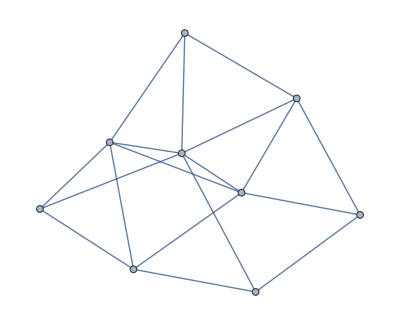
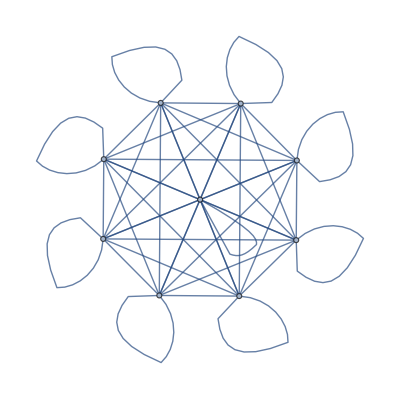
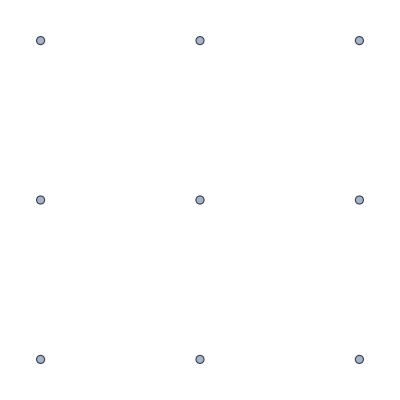
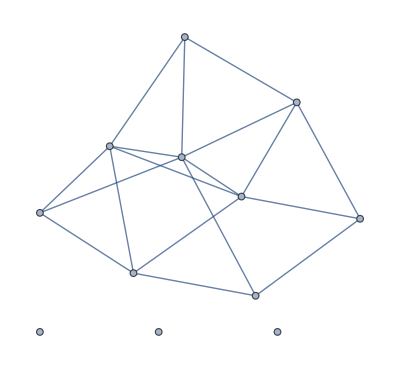
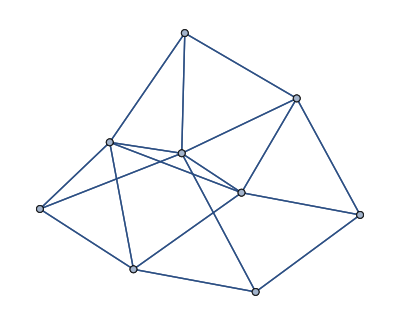
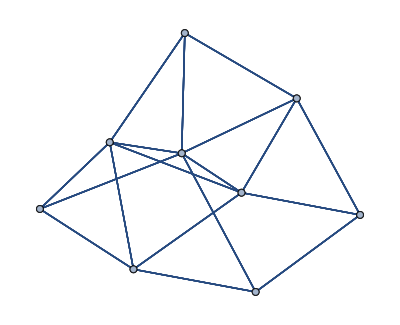
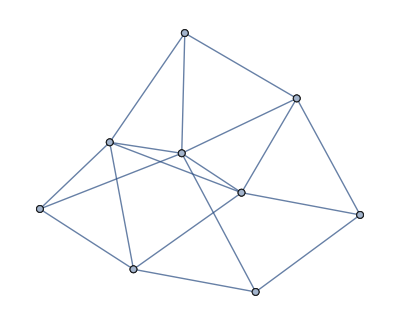
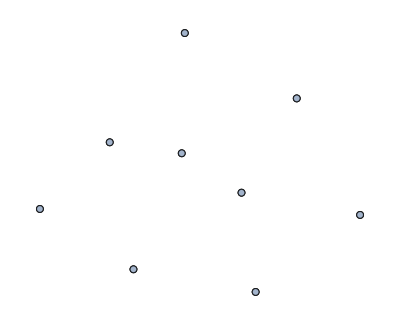
<|Boolean Graph Xor→-Graphics-,Boolean Graph Nand→-Graphics-,Graph Intersection→-Graphics-,Graph Union→-Graphics-,Graph Difference→-Graphics-,Graph Disjoint Union→-Graphics-,Cartesian Graph Product→-Graphics-,Conormal Graph Product→-Graphics-,Lexicographical Graph Product→-Graphics-,Normal Graph Product→-Graphics-,Rooted Graph Product→-Graphics-,Tensor Graph Product→-Graphics-,Graph Join→-Graphics-,Graph Sum→-Graphics-|>

```mathematica
AssociationThread[{"Boolean Graph Xor","Boolean Graph Nand","Graph Intersection","Graph Union","Graph Difference","Graph Disjoint Union","Cartesian Graph Product","Conormal Graph Product","Lexicographical Graph Product","Normal Graph Product","Rooted Graph Product","Tensor Graph Product","Graph Join","Graph Sum"},Map[(graphOperation↦graphOperation[graph,Graph[{2,3,5},{}]]),{BooleanGraph[Xor,##]&,BooleanGraph[Nand,##]&,GraphIntersection,GraphUnion,GraphDifference,GraphDisjointUnion,GraphProduct[##,"Cartesian"]&,GraphProduct[##,"Conormal"]&,GraphProduct[##,"Lexicographical"]&,GraphProduct[##,"Normal"]&,GraphProduct[##,"Rooted"]&,GraphProduct[##,"Tensor"]&,GraphJoin,GraphSum}]]
```

## Edge vector matrix graph formulation

```mathematica
UndirectedChinesePostmanProblem[graph_?GraphQ]:=Block[{weight,decisionvector,oddnodes,oddsubsets,order,oddorder,blossominequalities},weight=AnnotationValue[graph,EdgeWeight];
decisionvector=Array[Indexed[x,#]&,EdgeCount[graph]];
order=VertexCount[graph];
oddnodes=VertexList[graph,u_/;OddQ[VertexDegree[graph,u]]];oddorder=If[EvenQ[order],order-1,order];oddsubsets=Subsets[OddNodes[graph],{1,oddorder,2}];blossominequalities=Map[Function[set,Total[Indexed[x,First[Position[EdgeList[graph],#]]]&/@EdgeList[graph,x_<->y_/;((MemberQ[set,x]∧FreeQ[set,y])∨(FreeQ[set,x]∧MemberQ[set,y]))]]>=1],oddsubsets];LinearOptimization[weight.decisionvector,Join[blossominequalities,{Element[decisionvector,NonNegativeIntegers]}],decisionvector];
LinearOptimization[weight.decisionvector,{Element[decisionvector,NonNegativeIntegers]},decisionvector]]
```

```mathematica
UndirectedChinesePostmanProblem[graph]
```

{x1→0,x2→0,x3→0,x4→0,x5→0,x6→0,x7→0,x8→0,x9→0,x10→0,x11→0,x12→0,x13→0,x14→0,x15→0,x16→0,x17→0,x18→0}

```mathematica
UndirectedChinesePostmanProblem[graph][[All,-1]]
```

{1,0,0,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0}

```mathematica
Position[UndirectedChinesePostmanProblem[graph][[All,-1]],1]
```

{{1},{7},{10},{15}}

```mathematica
Extract[EdgeList[graph],Position[UndirectedChinesePostmanProblem[graph][[All,-1]],1]]
```

{1<->4,2<->6,3<->8,5<->7}

```mathematica
EulerianGraphQ[graph]
```

False

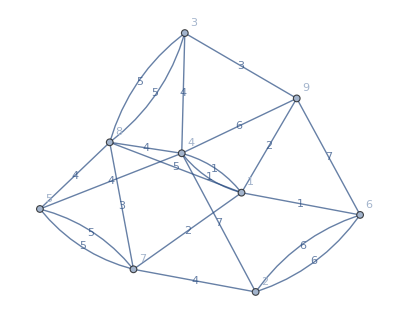

```mathematica
EdgeAdd[graph,Extract[EdgeList[graph],Position[UndirectedChinesePostmanProblem[graph][[All,-1]],1]]]
```

```mathematica
EulerianGraphQ[EdgeAdd[graph,Extract[EdgeList[graph],Position[UndirectedChinesePostmanProblem[graph][[All,-1]],1]]]]
```

False

```mathematica
VertexDegree[EdgeAdd[graph,Extract[EdgeList[graph],Position[UndirectedChinesePostmanProblem[graph][[All,-1]],1]]]]
```

{6,4,4,7,4,4,5,6,4}

```mathematica
decisionvector
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18}

```mathematica
Element[decisionvector,Integers]
```

(x1|x2|x3|x4|x5|x6|x7|x8|x9|x10|x11|x12|x13|x14|x15|x16|x17|x18)∈ℤ

```mathematica
IncidenceList[graph,{2,3,5}]
```

{2<->4,2<->6,2<->7,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8}

```mathematica
EdgeList[graph,x_<->y_/;((MemberQ[{1,2,3},x]∧FreeQ[{1,2,3},y])∨(FreeQ[{1,2,3},x]∧MemberQ[{1,2,3},y]))]
```

{1<->4,1<->6,1<->7,1<->8,1<->9,2<->4,2<->6,2<->7,3<->4,3<->8,3<->9}

```mathematica
Position[EdgeList[graph],1<->4]
```

{{1}}

```mathematica
Indexed[x,First[Position[EdgeList[graph],#]]]&/@{1<->4,1<->6,1<->7,1<->8,1<->9}
```

{x1,x2,x3,x4,x5}

```mathematica
AssociationMap[Function[set,EdgeList[graph,x_<->y_/;((MemberQ[set,x]∧FreeQ[set,y])∨(FreeQ[set,x]∧MemberQ[set,y]))]],Subsets[VertexList[graph],{1,9,2}]]
```

<|{1}→{1<->4,1<->6,1<->7,1<->8,1<->9},{2}→{2<->4,2<->6,2<->7},{3}→{3<->4,3<->8,3<->9},{4}→{1<->4,2<->4,3<->4,4<->5,4<->8,4<->9},{5}→{4<->5,5<->7,5<->8},{6}→{1<->6,2<->6,6<->9},{7}→{1<->7,2<->7,5<->7,7<->8},{8}→{1<->8,3<->8,4<->8,5<->8,7<->8},{9}→{1<->9,3<->9,4<->9,6<->9},{1,2,3}→{1<->4,1<->6,1<->7,1<->8,1<->9,2<->4,2<->6,2<->7,3<->4,3<->8,3<->9},{1,2,4}→{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,3<->4,4<->5,4<->8,4<->9},{1,2,5}→{1<->4,1<->6,1<->7,1<->8,1<->9,2<->4,2<->6,2<->7,4<->5,5<->7,5<->8},{1,2,6}→{1<->4,1<->7,1<->8,1<->9,2<->4,2<->7,6<->9},{1,2,7}→{1<->4,1<->6,1<->8,1<->9,2<->4,2<->6,5<->7,7<->8},{1,2,8}→{1<->4,1<->6,1<->7,1<->9,2<->4,2<->6,2<->7,3<->8,4<->8,5<->8,7<->8},{1,2,9}→{1<->4,1<->6,1<->7,1<->8,2<->4,2<->6,2<->7,3<->9,4<->9,6<->9},{1,3,4}→{1<->6,1<->7,1<->8,1<->9,2<->4,3<->8,3<->9,4<->5,4<->8,4<->9},{1,3,5}→{1<->4,1<->6,1<->7,1<->8,1<->9,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8},{1,3,6}→{1<->4,1<->7,1<->8,1<->9,2<->6,3<->4,3<->8,3<->9,6<->9},{1,3,7}→{1<->4,1<->6,1<->8,1<->9,2<->7,3<->4,3<->8,3<->9,5<->7,7<->8},{1,3,8}→{1<->4,1<->6,1<->7,1<->9,3<->4,3<->9,4<->8,5<->8,7<->8},{1,3,9}→{1<->4,1<->6,1<->7,1<->8,3<->4,3<->8,4<->9,6<->9},{1,4,5}→{1<->6,1<->7,1<->8,1<->9,2<->4,3<->4,4<->8,4<->9,5<->7,5<->8},{1,4,6}→{1<->7,1<->8,1<->9,2<->4,2<->6,3<->4,4<->5,4<->8,4<->9,6<->9},{1,4,7}→{1<->6,1<->8,1<->9,2<->4,2<->7,3<->4,4<->5,4<->8,4<->9,5<->7,7<->8},{1,4,8}→{1<->6,1<->7,1<->9,2<->4,3<->4,3<->8,4<->5,4<->9,5<->8,7<->8},{1,4,9}→{1<->6,1<->7,1<->8,2<->4,3<->4,3<->9,4<->5,4<->8,6<->9},{1,5,6}→{1<->4,1<->7,1<->8,1<->9,2<->6,4<->5,5<->7,5<->8,6<->9},{1,5,7}→{1<->4,1<->6,1<->8,1<->9,2<->7,4<->5,5<->8,7<->8},{1,5,8}→{1<->4,1<->6,1<->7,1<->9,3<->8,4<->5,4<->8,5<->7,7<->8},{1,5,9}→{1<->4,1<->6,1<->7,1<->8,3<->9,4<->5,4<->9,5<->7,5<->8,6<->9},{1,6,7}→{1<->4,1<->8,1<->9,2<->6,2<->7,5<->7,6<->9,7<->8},{1,6,8}→{1<->4,1<->7,1<->9,2<->6,3<->8,4<->8,5<->8,6<->9,7<->8},{1,6,9}→{1<->4,1<->7,1<->8,2<->6,3<->9,4<->9},{1,7,8}→{1<->4,1<->6,1<->9,2<->7,3<->8,4<->8,5<->7,5<->8},{1,7,9}→{1<->4,1<->6,1<->8,2<->7,3<->9,4<->9,5<->7,6<->9,7<->8},{1,8,9}→{1<->4,1<->6,1<->7,3<->8,3<->9,4<->8,4<->9,5<->8,6<->9,7<->8},{2,3,4}→{1<->4,2<->6,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9},{2,3,5}→{2<->4,2<->6,2<->7,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8},{2,3,6}→{1<->6,2<->4,2<->7,3<->4,3<->8,3<->9,6<->9},{2,3,7}→{1<->7,2<->4,2<->6,3<->4,3<->8,3<->9,5<->7,7<->8},{2,3,8}→{1<->8,2<->4,2<->6,2<->7,3<->4,3<->9,4<->8,5<->8,7<->8},{2,3,9}→{1<->9,2<->4,2<->6,2<->7,3<->4,3<->8,4<->9,6<->9},{2,4,5}→{1<->4,2<->6,2<->7,3<->4,4<->8,4<->9,5<->7,5<->8},{2,4,6}→{1<->4,1<->6,2<->7,3<->4,4<->5,4<->8,4<->9,6<->9},{2,4,7}→{1<->4,1<->7,2<->6,3<->4,4<->5,4<->8,4<->9,5<->7,7<->8},{2,4,8}→{1<->4,1<->8,2<->6,2<->7,3<->4,3<->8,4<->5,4<->9,5<->8,7<->8},{2,4,9}→{1<->4,1<->9,2<->6,2<->7,3<->4,3<->9,4<->5,4<->8,6<->9},{2,5,6}→{1<->6,2<->4,2<->7,4<->5,5<->7,5<->8,6<->9},{2,5,7}→{1<->7,2<->4,2<->6,4<->5,5<->8,7<->8},{2,5,8}→{1<->8,2<->4,2<->6,2<->7,3<->8,4<->5,4<->8,5<->7,7<->8},{2,5,9}→{1<->9,2<->4,2<->6,2<->7,3<->9,4<->5,4<->9,5<->7,5<->8,6<->9},{2,6,7}→{1<->6,1<->7,2<->4,5<->7,6<->9,7<->8},{2,6,8}→{1<->6,1<->8,2<->4,2<->7,3<->8,4<->8,5<->8,6<->9,7<->8},{2,6,9}→{1<->6,1<->9,2<->4,2<->7,3<->9,4<->9},{2,7,8}→{1<->7,1<->8,2<->4,2<->6,3<->8,4<->8,5<->7,5<->8},{2,7,9}→{1<->7,1<->9,2<->4,2<->6,3<->9,4<->9,5<->7,6<->9,7<->8},{2,8,9}→{1<->8,1<->9,2<->4,2<->6,2<->7,3<->8,3<->9,4<->8,4<->9,5<->8,6<->9,7<->8},{3,4,5}→{1<->4,2<->4,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8},{3,4,6}→{1<->4,1<->6,2<->4,2<->6,3<->8,3<->9,4<->5,4<->8,4<->9,6<->9},{3,4,7}→{1<->4,1<->7,2<->4,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,7<->8},{3,4,8}→{1<->4,1<->8,2<->4,3<->9,4<->5,4<->9,5<->8,7<->8},{3,4,9}→{1<->4,1<->9,2<->4,3<->8,4<->5,4<->8,6<->9},{3,5,6}→{1<->6,2<->6,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8,6<->9},{3,5,7}→{1<->7,2<->7,3<->4,3<->8,3<->9,4<->5,5<->8,7<->8},{3,5,8}→{1<->8,3<->4,3<->9,4<->5,4<->8,5<->7,7<->8},{3,5,9}→{1<->9,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8,6<->9},{3,6,7}→{1<->6,1<->7,2<->6,2<->7,3<->4,3<->8,3<->9,5<->7,6<->9,7<->8},{3,6,8}→{1<->6,1<->8,2<->6,3<->4,3<->9,4<->8,5<->8,6<->9,7<->8},{3,6,9}→{1<->6,1<->9,2<->6,3<->4,3<->8,4<->9},{3,7,8}→{1<->7,1<->8,2<->7,3<->4,3<->9,4<->8,5<->7,5<->8},{3,7,9}→{1<->7,1<->9,2<->7,3<->4,3<->8,4<->9,5<->7,6<->9,7<->8},{3,8,9}→{1<->8,1<->9,3<->4,4<->8,4<->9,5<->8,6<->9,7<->8},{4,5,6}→{1<->4,1<->6,2<->4,2<->6,3<->4,4<->8,4<->9,5<->7,5<->8,6<->9},{4,5,7}→{1<->4,1<->7,2<->4,2<->7,3<->4,4<->8,4<->9,5<->8,7<->8},{4,5,8}→{1<->4,1<->8,2<->4,3<->4,3<->8,4<->9,5<->7,7<->8},{4,5,9}→{1<->4,1<->9,2<->4,3<->4,3<->9,4<->8,5<->7,5<->8,6<->9},{4,6,7}→{1<->4,1<->6,1<->7,2<->4,2<->6,2<->7,3<->4,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{4,6,8}→{1<->4,1<->6,1<->8,2<->4,2<->6,3<->4,3<->8,4<->5,4<->9,5<->8,6<->9,7<->8},{4,6,9}→{1<->4,1<->6,1<->9,2<->4,2<->6,3<->4,3<->9,4<->5,4<->8},{4,7,8}→{1<->4,1<->7,1<->8,2<->4,2<->7,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8},{4,7,9}→{1<->4,1<->7,1<->9,2<->4,2<->7,3<->4,3<->9,4<->5,4<->8,5<->7,6<->9,7<->8},{4,8,9}→{1<->4,1<->8,1<->9,2<->4,3<->4,3<->8,3<->9,4<->5,5<->8,6<->9,7<->8},{5,6,7}→{1<->6,1<->7,2<->6,2<->7,4<->5,5<->8,6<->9,7<->8},{5,6,8}→{1<->6,1<->8,2<->6,3<->8,4<->5,4<->8,5<->7,6<->9,7<->8},{5,6,9}→{1<->6,1<->9,2<->6,3<->9,4<->5,4<->9,5<->7,5<->8},{5,7,8}→{1<->7,1<->8,2<->7,3<->8,4<->5,4<->8},{5,7,9}→{1<->7,1<->9,2<->7,3<->9,4<->5,4<->9,5<->8,6<->9,7<->8},{5,8,9}→{1<->8,1<->9,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{6,7,8}→{1<->6,1<->7,1<->8,2<->6,2<->7,3<->8,4<->8,5<->7,5<->8,6<->9},{6,7,9}→{1<->6,1<->7,1<->9,2<->6,2<->7,3<->9,4<->9,5<->7,7<->8},{6,8,9}→{1<->6,1<->8,1<->9,2<->6,3<->8,3<->9,4<->8,4<->9,5<->8,7<->8},{7,8,9}→{1<->7,1<->8,1<->9,2<->7,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8,6<->9},{1,2,3,4,5}→{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8},{1,2,3,4,6}→{1<->7,1<->8,1<->9,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9,6<->9},{1,2,3,4,7}→{1<->6,1<->8,1<->9,2<->6,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,7<->8},{1,2,3,4,8}→{1<->6,1<->7,1<->9,2<->6,2<->7,3<->9,4<->5,4<->9,5<->8,7<->8},{1,2,3,4,9}→{1<->6,1<->7,1<->8,2<->6,2<->7,3<->8,4<->5,4<->8,6<->9},{1,2,3,5,6}→{1<->4,1<->7,1<->8,1<->9,2<->4,2<->7,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8,6<->9},{1,2,3,5,7}→{1<->4,1<->6,1<->8,1<->9,2<->4,2<->6,3<->4,3<->8,3<->9,4<->5,5<->8,7<->8},{1,2,3,5,8}→{1<->4,1<->6,1<->7,1<->9,2<->4,2<->6,2<->7,3<->4,3<->9,4<->5,4<->8,5<->7,7<->8},{1,2,3,5,9}→{1<->4,1<->6,1<->7,1<->8,2<->4,2<->6,2<->7,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8,6<->9},{1,2,3,6,7}→{1<->4,1<->8,1<->9,2<->4,3<->4,3<->8,3<->9,5<->7,6<->9,7<->8},{1,2,3,6,8}→{1<->4,1<->7,1<->9,2<->4,2<->7,3<->4,3<->9,4<->8,5<->8,6<->9,7<->8},{1,2,3,6,9}→{1<->4,1<->7,1<->8,2<->4,2<->7,3<->4,3<->8,4<->9},{1,2,3,7,8}→{1<->4,1<->6,1<->9,2<->4,2<->6,3<->4,3<->9,4<->8,5<->7,5<->8},{1,2,3,7,9}→{1<->4,1<->6,1<->8,2<->4,2<->6,3<->4,3<->8,4<->9,5<->7,6<->9,7<->8},{1,2,3,8,9}→{1<->4,1<->6,1<->7,2<->4,2<->6,2<->7,3<->4,4<->8,4<->9,5<->8,6<->9,7<->8},{1,2,4,5,6}→{1<->7,1<->8,1<->9,2<->7,3<->4,4<->8,4<->9,5<->7,5<->8,6<->9},{1,2,4,5,7}→{1<->6,1<->8,1<->9,2<->6,3<->4,4<->8,4<->9,5<->8,7<->8},{1,2,4,5,8}→{1<->6,1<->7,1<->9,2<->6,2<->7,3<->4,3<->8,4<->9,5<->7,7<->8},{1,2,4,5,9}→{1<->6,1<->7,1<->8,2<->6,2<->7,3<->4,3<->9,4<->8,5<->7,5<->8,6<->9},{1,2,4,6,7}→{1<->8,1<->9,3<->4,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{1,2,4,6,8}→{1<->7,1<->9,2<->7,3<->4,3<->8,4<->5,4<->9,5<->8,6<->9,7<->8},{1,2,4,6,9}→{1<->7,1<->8,2<->7,3<->4,3<->9,4<->5,4<->8},{1,2,4,7,8}→{1<->6,1<->9,2<->6,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8},{1,2,4,7,9}→{1<->6,1<->8,2<->6,3<->4,3<->9,4<->5,4<->8,5<->7,6<->9,7<->8},{1,2,4,8,9}→{1<->6,1<->7,2<->6,2<->7,3<->4,3<->8,3<->9,4<->5,5<->8,6<->9,7<->8},{1,2,5,6,7}→{1<->4,1<->8,1<->9,2<->4,4<->5,5<->8,6<->9,7<->8},{1,2,5,6,8}→{1<->4,1<->7,1<->9,2<->4,2<->7,3<->8,4<->5,4<->8,5<->7,6<->9,7<->8},{1,2,5,6,9}→{1<->4,1<->7,1<->8,2<->4,2<->7,3<->9,4<->5,4<->9,5<->7,5<->8},{1,2,5,7,8}→{1<->4,1<->6,1<->9,2<->4,2<->6,3<->8,4<->5,4<->8},{1,2,5,7,9}→{1<->4,1<->6,1<->8,2<->4,2<->6,3<->9,4<->5,4<->9,5<->8,6<->9,7<->8},{1,2,5,8,9}→{1<->4,1<->6,1<->7,2<->4,2<->6,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{1,2,6,7,8}→{1<->4,1<->9,2<->4,3<->8,4<->8,5<->7,5<->8,6<->9},{1,2,6,7,9}→{1<->4,1<->8,2<->4,3<->9,4<->9,5<->7,7<->8},{1,2,6,8,9}→{1<->4,1<->7,2<->4,2<->7,3<->8,3<->9,4<->8,4<->9,5<->8,7<->8},{1,2,7,8,9}→{1<->4,1<->6,2<->4,2<->6,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8,6<->9},{1,3,4,5,6}→{1<->7,1<->8,1<->9,2<->4,2<->6,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8,6<->9},{1,3,4,5,7}→{1<->6,1<->8,1<->9,2<->4,2<->7,3<->8,3<->9,4<->8,4<->9,5<->8,7<->8},{1,3,4,5,8}→{1<->6,1<->7,1<->9,2<->4,3<->9,4<->9,5<->7,7<->8},{1,3,4,5,9}→{1<->6,1<->7,1<->8,2<->4,3<->8,4<->8,5<->7,5<->8,6<->9},{1,3,4,6,7}→{1<->8,1<->9,2<->4,2<->6,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{1,3,4,6,8}→{1<->7,1<->9,2<->4,2<->6,3<->9,4<->5,4<->9,5<->8,6<->9,7<->8},{1,3,4,6,9}→{1<->7,1<->8,2<->4,2<->6,3<->8,4<->5,4<->8},{1,3,4,7,8}→{1<->6,1<->9,2<->4,2<->7,3<->9,4<->5,4<->9,5<->7,5<->8},{1,3,4,7,9}→{1<->6,1<->8,2<->4,2<->7,3<->8,4<->5,4<->8,5<->7,6<->9,7<->8},{1,3,4,8,9}→{1<->6,1<->7,2<->4,4<->5,5<->8,6<->9,7<->8},{1,3,5,6,7}→{1<->4,1<->8,1<->9,2<->6,2<->7,3<->4,3<->8,3<->9,4<->5,5<->8,6<->9,7<->8},{1,3,5,6,8}→{1<->4,1<->7,1<->9,2<->6,3<->4,3<->9,4<->5,4<->8,5<->7,6<->9,7<->8},{1,3,5,6,9}→{1<->4,1<->7,1<->8,2<->6,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8},{1,3,5,7,8}→{1<->4,1<->6,1<->9,2<->7,3<->4,3<->9,4<->5,4<->8},{1,3,5,7,9}→{1<->4,1<->6,1<->8,2<->7,3<->4,3<->8,4<->5,4<->9,5<->8,6<->9,7<->8},{1,3,5,8,9}→{1<->4,1<->6,1<->7,3<->4,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{1,3,6,7,8}→{1<->4,1<->9,2<->6,2<->7,3<->4,3<->9,4<->8,5<->7,5<->8,6<->9},{1,3,6,7,9}→{1<->4,1<->8,2<->6,2<->7,3<->4,3<->8,4<->9,5<->7,7<->8},{1,3,6,8,9}→{1<->4,1<->7,2<->6,3<->4,4<->8,4<->9,5<->8,7<->8},{1,3,7,8,9}→{1<->4,1<->6,2<->7,3<->4,4<->8,4<->9,5<->7,5<->8,6<->9},{1,4,5,6,7}→{1<->8,1<->9,2<->4,2<->6,2<->7,3<->4,4<->8,4<->9,5<->8,6<->9,7<->8},{1,4,5,6,8}→{1<->7,1<->9,2<->4,2<->6,3<->4,3<->8,4<->9,5<->7,6<->9,7<->8},{1,4,5,6,9}→{1<->7,1<->8,2<->4,2<->6,3<->4,3<->9,4<->8,5<->7,5<->8},{1,4,5,7,8}→{1<->6,1<->9,2<->4,2<->7,3<->4,3<->8,4<->9},{1,4,5,7,9}→{1<->6,1<->8,2<->4,2<->7,3<->4,3<->9,4<->8,5<->8,6<->9,7<->8},{1,4,5,8,9}→{1<->6,1<->7,2<->4,3<->4,3<->8,3<->9,5<->7,6<->9,7<->8},{1,4,6,7,8}→{1<->9,2<->4,2<->6,2<->7,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8,6<->9},{1,4,6,7,9}→{1<->8,2<->4,2<->6,2<->7,3<->4,3<->9,4<->5,4<->8,5<->7,7<->8},{1,4,6,8,9}→{1<->7,2<->4,2<->6,3<->4,3<->8,3<->9,4<->5,5<->8,7<->8},{1,4,7,8,9}→{1<->6,2<->4,2<->7,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8,6<->9},{1,5,6,7,8}→{1<->4,1<->9,2<->6,2<->7,3<->8,4<->5,4<->8,6<->9},{1,5,6,7,9}→{1<->4,1<->8,2<->6,2<->7,3<->9,4<->5,4<->9,5<->8,7<->8},{1,5,6,8,9}→{1<->4,1<->7,2<->6,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,7<->8},{1,5,7,8,9}→{1<->4,1<->6,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9,6<->9},{1,6,7,8,9}→{1<->4,2<->6,2<->7,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8},{2,3,4,5,6}→{1<->4,1<->6,2<->7,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8,6<->9},{2,3,4,5,7}→{1<->4,1<->7,2<->6,3<->8,3<->9,4<->8,4<->9,5<->8,7<->8},{2,3,4,5,8}→{1<->4,1<->8,2<->6,2<->7,3<->9,4<->9,5<->7,7<->8},{2,3,4,5,9}→{1<->4,1<->9,2<->6,2<->7,3<->8,4<->8,5<->7,5<->8,6<->9},{2,3,4,6,7}→{1<->4,1<->6,1<->7,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{2,3,4,6,8}→{1<->4,1<->6,1<->8,2<->7,3<->9,4<->5,4<->9,5<->8,6<->9,7<->8},{2,3,4,6,9}→{1<->4,1<->6,1<->9,2<->7,3<->8,4<->5,4<->8},{2,3,4,7,8}→{1<->4,1<->7,1<->8,2<->6,3<->9,4<->5,4<->9,5<->7,5<->8},{2,3,4,7,9}→{1<->4,1<->7,1<->9,2<->6,3<->8,4<->5,4<->8,5<->7,6<->9,7<->8},{2,3,4,8,9}→{1<->4,1<->8,1<->9,2<->6,2<->7,4<->5,5<->8,6<->9,7<->8},{2,3,5,6,7}→{1<->6,1<->7,2<->4,3<->4,3<->8,3<->9,4<->5,5<->8,6<->9,7<->8},{2,3,5,6,8}→{1<->6,1<->8,2<->4,2<->7,3<->4,3<->9,4<->5,4<->8,5<->7,6<->9,7<->8},{2,3,5,6,9}→{1<->6,1<->9,2<->4,2<->7,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8},{2,3,5,7,8}→{1<->7,1<->8,2<->4,2<->6,3<->4,3<->9,4<->5,4<->8},{2,3,5,7,9}→{1<->7,1<->9,2<->4,2<->6,3<->4,3<->8,4<->5,4<->9,5<->8,6<->9,7<->8},{2,3,5,8,9}→{1<->8,1<->9,2<->4,2<->6,2<->7,3<->4,4<->5,4<->8,4<->9,5<->7,6<->9,7<->8},{2,3,6,7,8}→{1<->6,1<->7,1<->8,2<->4,3<->4,3<->9,4<->8,5<->7,5<->8,6<->9},{2,3,6,7,9}→{1<->6,1<->7,1<->9,2<->4,3<->4,3<->8,4<->9,5<->7,7<->8},{2,3,6,8,9}→{1<->6,1<->8,1<->9,2<->4,2<->7,3<->4,4<->8,4<->9,5<->8,7<->8},{2,3,7,8,9}→{1<->7,1<->8,1<->9,2<->4,2<->6,3<->4,4<->8,4<->9,5<->7,5<->8,6<->9},{2,4,5,6,7}→{1<->4,1<->6,1<->7,3<->4,4<->8,4<->9,5<->8,6<->9,7<->8},{2,4,5,6,8}→{1<->4,1<->6,1<->8,2<->7,3<->4,3<->8,4<->9,5<->7,6<->9,7<->8},{2,4,5,6,9}→{1<->4,1<->6,1<->9,2<->7,3<->4,3<->9,4<->8,5<->7,5<->8},{2,4,5,7,8}→{1<->4,1<->7,1<->8,2<->6,3<->4,3<->8,4<->9},{2,4,5,7,9}→{1<->4,1<->7,1<->9,2<->6,3<->4,3<->9,4<->8,5<->8,6<->9,7<->8},{2,4,5,8,9}→{1<->4,1<->8,1<->9,2<->6,2<->7,3<->4,3<->8,3<->9,5<->7,6<->9,7<->8},{2,4,6,7,8}→{1<->4,1<->6,1<->7,1<->8,3<->4,3<->8,4<->5,4<->9,5<->7,5<->8,6<->9},{2,4,6,7,9}→{1<->4,1<->6,1<->7,1<->9,3<->4,3<->9,4<->5,4<->8,5<->7,7<->8},{2,4,6,8,9}→{1<->4,1<->6,1<->8,1<->9,2<->7,3<->4,3<->8,3<->9,4<->5,5<->8,7<->8},{2,4,7,8,9}→{1<->4,1<->7,1<->8,1<->9,2<->6,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8,6<->9},{2,5,6,7,8}→{1<->6,1<->7,1<->8,2<->4,3<->8,4<->5,4<->8,6<->9},{2,5,6,7,9}→{1<->6,1<->7,1<->9,2<->4,3<->9,4<->5,4<->9,5<->8,7<->8},{2,5,6,8,9}→{1<->6,1<->8,1<->9,2<->4,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9,5<->7,7<->8},{2,5,7,8,9}→{1<->7,1<->8,1<->9,2<->4,2<->6,3<->8,3<->9,4<->5,4<->8,4<->9,6<->9},{2,6,7,8,9}→{1<->6,1<->7,1<->8,1<->9,2<->4,3<->8,3<->9,4<->8,4<->9,5<->7,5<->8},{3,4,5,6,7}→{1<->4,1<->6,1<->7,2<->4,2<->6,2<->7,3<->8,3<->9,4<->8,4<->9,5<->8,6<->9,7<->8},{3,4,5,6,8}→{1<->4,1<->6,1<->8,2<->4,2<->6,3<->9,4<->9,5<->7,6<->9,7<->8},{3,4,5,6,9}→{1<->4,1<->6,1<->9,2<->4,2<->6,3<->8,4<->8,5<->7,5<->8},{3,4,5,7,8}→{1<->4,1<->7,1<->8,2<->4,2<->7,3<->9,4<->9},{3,4,5,7,9}→{1<->4,1<->7,1<->9,2<->4,2<->7,3<->8,4<->8,5<->8,6<->9,7<->8},{3,4,5,8,9}→{1<->4,1<->8,1<->9,2<->4,5<->7,6<->9,7<->8},{3,4,6,7,8}→{1<->4,1<->6,1<->7,1<->8,2<->4,2<->6,2<->7,3<->9,4<->5,4<->9,5<->7,5<->8,6<->9},{3,4,6,7,9}→{1<->4,1<->6,1<->7,1<->9,2<->4,2<->6,2<->7,3<->8,4<->5,4<->8,5<->7,7<->8},{3,4,6,8,9}→{1<->4,1<->6,1<->8,1<->9,2<->4,2<->6,4<->5,5<->8,7<->8},{3,4,7,8,9}→{1<->4,1<->7,1<->8,1<->9,2<->4,2<->7,4<->5,5<->7,5<->8,6<->9},{3,5,6,7,8}→{1<->6,1<->7,1<->8,2<->6,2<->7,3<->4,3<->9,4<->5,4<->8,6<->9},{3,5,6,7,9}→{1<->6,1<->7,1<->9,2<->6,2<->7,3<->4,3<->8,4<->5,4<->9,5<->8,7<->8},{3,5,6,8,9}→{1<->6,1<->8,1<->9,2<->6,3<->4,4<->5,4<->8,4<->9,5<->7,7<->8},{3,5,7,8,9}→{1<->7,1<->8,1<->9,2<->7,3<->4,4<->5,4<->8,4<->9,6<->9},{3,6,7,8,9}→{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,3<->4,4<->8,4<->9,5<->7,5<->8},{4,5,6,7,8}→{1<->4,1<->6,1<->7,1<->8,2<->4,2<->6,2<->7,3<->4,3<->8,4<->9,6<->9},{4,5,6,7,9}→{1<->4,1<->6,1<->7,1<->9,2<->4,2<->6,2<->7,3<->4,3<->9,4<->8,5<->8,7<->8},{4,5,6,8,9}→{1<->4,1<->6,1<->8,1<->9,2<->4,2<->6,3<->4,3<->8,3<->9,5<->7,7<->8},{4,5,7,8,9}→{1<->4,1<->7,1<->8,1<->9,2<->4,2<->7,3<->4,3<->8,3<->9,6<->9},{4,6,7,8,9}→{1<->4,1<->6,1<->7,1<->8,1<->9,2<->4,2<->6,2<->7,3<->4,3<->8,3<->9,4<->5,5<->7,5<->8},{5,6,7,8,9}→{1<->6,1<->7,1<->8,1<->9,2<->6,2<->7,3<->8,3<->9,4<->5,4<->8,4<->9},{1,2,3,4,5,6,7}→{1<->8,1<->9,3<->8,3<->9,4<->8,4<->9,5<->8,6<->9,7<->8},{1,2,3,4,5,6,8}→{1<->7,1<->9,2<->7,3<->9,4<->9,5<->7,6<->9,7<->8},{1,2,3,4,5,6,9}→{1<->7,1<->8,2<->7,3<->8,4<->8,5<->7,5<->8},{1,2,3,4,5,7,8}→{1<->6,1<->9,2<->6,3<->9,4<->9},{1,2,3,4,5,7,9}→{1<->6,1<->8,2<->6,3<->8,4<->8,5<->8,6<->9,7<->8},{1,2,3,4,5,8,9}→{1<->6,1<->7,2<->6,2<->7,5<->7,6<->9,7<->8},{1,2,3,4,6,7,8}→{1<->9,3<->9,4<->5,4<->9,5<->7,5<->8,6<->9},{1,2,3,4,6,7,9}→{1<->8,3<->8,4<->5,4<->8,5<->7,7<->8},{1,2,3,4,6,8,9}→{1<->7,2<->7,4<->5,5<->8,7<->8},{1,2,3,4,7,8,9}→{1<->6,2<->6,4<->5,5<->7,5<->8,6<->9},{1,2,3,5,6,7,8}→{1<->4,1<->9,2<->4,3<->4,3<->9,4<->5,4<->8,6<->9},{1,2,3,5,6,7,9}→{1<->4,1<->8,2<->4,3<->4,3<->8,4<->5,4<->9,5<->8,7<->8},{1,2,3,5,6,8,9}→{1<->4,1<->7,2<->4,2<->7,3<->4,4<->5,4<->8,4<->9,5<->7,7<->8},{1,2,3,5,7,8,9}→{1<->4,1<->6,2<->4,2<->6,3<->4,4<->5,4<->8,4<->9,6<->9},{1,2,3,6,7,8,9}→{1<->4,2<->4,3<->4,4<->8,4<->9,5<->7,5<->8},{1,2,4,5,6,7,8}→{1<->9,3<->4,3<->8,4<->9,6<->9},{1,2,4,5,6,7,9}→{1<->8,3<->4,3<->9,4<->8,5<->8,7<->8},{1,2,4,5,6,8,9}→{1<->7,2<->7,3<->4,3<->8,3<->9,5<->7,7<->8},{1,2,4,5,7,8,9}→{1<->6,2<->6,3<->4,3<->8,3<->9,6<->9},{1,2,4,6,7,8,9}→{3<->4,3<->8,3<->9,4<->5,5<->7,5<->8},{1,2,5,6,7,8,9}→{1<->4,2<->4,3<->8,3<->9,4<->5,4<->8,4<->9},{1,3,4,5,6,7,8}→{1<->9,2<->4,2<->6,2<->7,3<->9,4<->9,6<->9},{1,3,4,5,6,7,9}→{1<->8,2<->4,2<->6,2<->7,3<->8,4<->8,5<->8,7<->8},{1,3,4,5,6,8,9}→{1<->7,2<->4,2<->6,5<->7,7<->8},{1,3,4,5,7,8,9}→{1<->6,2<->4,2<->7,6<->9},{1,3,4,6,7,8,9}→{2<->4,2<->6,2<->7,4<->5,5<->7,5<->8},{1,3,5,6,7,8,9}→{1<->4,2<->6,2<->7,3<->4,4<->5,4<->8,4<->9},{1,4,5,6,7,8,9}→{2<->4,2<->6,2<->7,3<->4,3<->8,3<->9},{2,3,4,5,6,7,8}→{1<->4,1<->6,1<->7,1<->8,3<->9,4<->9,6<->9},{2,3,4,5,6,7,9}→{1<->4,1<->6,1<->7,1<->9,3<->8,4<->8,5<->8,7<->8},{2,3,4,5,6,8,9}→{1<->4,1<->6,1<->8,1<->9,2<->7,5<->7,7<->8},{2,3,4,5,7,8,9}→{1<->4,1<->7,1<->8,1<->9,2<->6,6<->9},{2,3,4,6,7,8,9}→{1<->4,1<->6,1<->7,1<->8,1<->9,4<->5,5<->7,5<->8},{2,3,5,6,7,8,9}→{1<->6,1<->7,1<->8,1<->9,2<->4,3<->4,4<->5,4<->8,4<->9},{2,4,5,6,7,8,9}→{1<->4,1<->6,1<->7,1<->8,1<->9,3<->4,3<->8,3<->9},{3,4,5,6,7,8,9}→{1<->4,1<->6,1<->7,1<->8,1<->9,2<->4,2<->6,2<->7},{1,2,3,4,5,6,7,8,9}→{}|>

```mathematica
AssociationMap[Function[set,Total[Indexed[x,First[Position[EdgeList[graph],#]]]&/@EdgeList[graph,x_<->y_/;((MemberQ[set,x]∧FreeQ[set,y])∨(FreeQ[set,x]∧MemberQ[set,y]))]]>=1],Subsets[VertexList[graph],{1,9,2}]]
```

<|{1}→x1+x2+x3+x4+x5≥1,{2}→x6+x7+x8≥1,{3}→x9+x10+x11≥1,{4}→x1+x6+x9+x12+x13+x14≥1,{5}→x12+x15+x16≥1,{6}→x2+x7+x17≥1,{7}→x3+x8+x15+x18≥1,{8}→x4+x10+x13+x16+x18≥1,{9}→x5+x11+x14+x17≥1,{1,2,3}→x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11≥1,{1,2,4}→x2+x3+x4+x5+x7+x8+x9+x12+x13+x14≥1,{1,2,5}→x1+x2+x3+x4+x5+x6+x7+x8+x12+x15+x16≥1,{1,2,6}→x1+x3+x4+x5+x6+x8+x17≥1,{1,2,7}→x1+x2+x4+x5+x6+x7+x15+x18≥1,{1,2,8}→x1+x2+x3+x5+x6+x7+x8+x10+x13+x16+x18≥1,{1,2,9}→x1+x2+x3+x4+x6+x7+x8+x11+x14+x17≥1,{1,3,4}→x2+x3+x4+x5+x6+x10+x11+x12+x13+x14≥1,{1,3,5}→x1+x2+x3+x4+x5+x9+x10+x11+x12+x15+x16≥1,{1,3,6}→x1+x3+x4+x5+x7+x9+x10+x11+x17≥1,{1,3,7}→x1+x2+x4+x5+x8+x9+x10+x11+x15+x18≥1,{1,3,8}→x1+x2+x3+x5+x9+x11+x13+x16+x18≥1,{1,3,9}→x1+x2+x3+x4+x9+x10+x14+x17≥1,{1,4,5}→x2+x3+x4+x5+x6+x9+x13+x14+x15+x16≥1,{1,4,6}→x3+x4+x5+x6+x7+x9+x12+x13+x14+x17≥1,{1,4,7}→x2+x4+x5+x6+x8+x9+x12+x13+x14+x15+x18≥1,{1,4,8}→x2+x3+x5+x6+x9+x10+x12+x14+x16+x18≥1,{1,4,9}→x2+x3+x4+x6+x9+x11+x12+x13+x17≥1,{1,5,6}→x1+x3+x4+x5+x7+x12+x15+x16+x17≥1,{1,5,7}→x1+x2+x4+x5+x8+x12+x16+x18≥1,{1,5,8}→x1+x2+x3+x5+x10+x12+x13+x15+x18≥1,{1,5,9}→x1+x2+x3+x4+x11+x12+x14+x15+x16+x17≥1,{1,6,7}→x1+x4+x5+x7+x8+x15+x17+x18≥1,{1,6,8}→x1+x3+x5+x7+x10+x13+x16+x17+x18≥1,{1,6,9}→x1+x3+x4+x7+x11+x14≥1,{1,7,8}→x1+x2+x5+x8+x10+x13+x15+x16≥1,{1,7,9}→x1+x2+x4+x8+x11+x14+x15+x17+x18≥1,{1,8,9}→x1+x2+x3+x10+x11+x13+x14+x16+x17+x18≥1,{2,3,4}→x1+x7+x8+x10+x11+x12+x13+x14≥1,{2,3,5}→x6+x7+x8+x9+x10+x11+x12+x15+x16≥1,{2,3,6}→x2+x6+x8+x9+x10+x11+x17≥1,{2,3,7}→x3+x6+x7+x9+x10+x11+x15+x18≥1,{2,3,8}→x4+x6+x7+x8+x9+x11+x13+x16+x18≥1,{2,3,9}→x5+x6+x7+x8+x9+x10+x14+x17≥1,{2,4,5}→x1+x7+x8+x9+x13+x14+x15+x16≥1,{2,4,6}→x1+x2+x8+x9+x12+x13+x14+x17≥1,{2,4,7}→x1+x3+x7+x9+x12+x13+x14+x15+x18≥1,{2,4,8}→x1+x4+x7+x8+x9+x10+x12+x14+x16+x18≥1,{2,4,9}→x1+x5+x7+x8+x9+x11+x12+x13+x17≥1,{2,5,6}→x2+x6+x8+x12+x15+x16+x17≥1,{2,5,7}→x3+x6+x7+x12+x16+x18≥1,{2,5,8}→x4+x6+x7+x8+x10+x12+x13+x15+x18≥1,{2,5,9}→x5+x6+x7+x8+x11+x12+x14+x15+x16+x17≥1,{2,6,7}→x2+x3+x6+x15+x17+x18≥1,{2,6,8}→x2+x4+x6+x8+x10+x13+x16+x17+x18≥1,{2,6,9}→x2+x5+x6+x8+x11+x14≥1,{2,7,8}→x3+x4+x6+x7+x10+x13+x15+x16≥1,{2,7,9}→x3+x5+x6+x7+x11+x14+x15+x17+x18≥1,{2,8,9}→x4+x5+x6+x7+x8+x10+x11+x13+x14+x16+x17+x18≥1,{3,4,5}→x1+x6+x10+x11+x13+x14+x15+x16≥1,{3,4,6}→x1+x2+x6+x7+x10+x11+x12+x13+x14+x17≥1,{3,4,7}→x1+x3+x6+x8+x10+x11+x12+x13+x14+x15+x18≥1,{3,4,8}→x1+x4+x6+x11+x12+x14+x16+x18≥1,{3,4,9}→x1+x5+x6+x10+x12+x13+x17≥1,{3,5,6}→x2+x7+x9+x10+x11+x12+x15+x16+x17≥1,{3,5,7}→x3+x8+x9+x10+x11+x12+x16+x18≥1,{3,5,8}→x4+x9+x11+x12+x13+x15+x18≥1,{3,5,9}→x5+x9+x10+x12+x14+x15+x16+x17≥1,{3,6,7}→x2+x3+x7+x8+x9+x10+x11+x15+x17+x18≥1,{3,6,8}→x2+x4+x7+x9+x11+x13+x16+x17+x18≥1,{3,6,9}→x2+x5+x7+x9+x10+x14≥1,{3,7,8}→x3+x4+x8+x9+x11+x13+x15+x16≥1,{3,7,9}→x3+x5+x8+x9+x10+x14+x15+x17+x18≥1,{3,8,9}→x4+x5+x9+x13+x14+x16+x17+x18≥1,{4,5,6}→x1+x2+x6+x7+x9+x13+x14+x15+x16+x17≥1,{4,5,7}→x1+x3+x6+x8+x9+x13+x14+x16+x18≥1,{4,5,8}→x1+x4+x6+x9+x10+x14+x15+x18≥1,{4,5,9}→x1+x5+x6+x9+x11+x13+x15+x16+x17≥1,{4,6,7}→x1+x2+x3+x6+x7+x8+x9+x12+x13+x14+x15+x17+x18≥1,{4,6,8}→x1+x2+x4+x6+x7+x9+x10+x12+x14+x16+x17+x18≥1,{4,6,9}→x1+x2+x5+x6+x7+x9+x11+x12+x13≥1,{4,7,8}→x1+x3+x4+x6+x8+x9+x10+x12+x14+x15+x16≥1,{4,7,9}→x1+x3+x5+x6+x8+x9+x11+x12+x13+x15+x17+x18≥1,{4,8,9}→x1+x4+x5+x6+x9+x10+x11+x12+x16+x17+x18≥1,{5,6,7}→x2+x3+x7+x8+x12+x16+x17+x18≥1,{5,6,8}→x2+x4+x7+x10+x12+x13+x15+x17+x18≥1,{5,6,9}→x2+x5+x7+x11+x12+x14+x15+x16≥1,{5,7,8}→x3+x4+x8+x10+x12+x13≥1,{5,7,9}→x3+x5+x8+x11+x12+x14+x16+x17+x18≥1,{5,8,9}→x4+x5+x10+x11+x12+x13+x14+x15+x17+x18≥1,{6,7,8}→x2+x3+x4+x7+x8+x10+x13+x15+x16+x17≥1,{6,7,9}→x2+x3+x5+x7+x8+x11+x14+x15+x18≥1,{6,8,9}→x2+x4+x5+x7+x10+x11+x13+x14+x16+x18≥1,{7,8,9}→x3+x4+x5+x8+x10+x11+x13+x14+x15+x16+x17≥1,{1,2,3,4,5}→x2+x3+x4+x5+x7+x8+x10+x11+x13+x14+x15+x16≥1,{1,2,3,4,6}→x3+x4+x5+x8+x10+x11+x12+x13+x14+x17≥1,{1,2,3,4,7}→x2+x4+x5+x7+x10+x11+x12+x13+x14+x15+x18≥1,{1,2,3,4,8}→x2+x3+x5+x7+x8+x11+x12+x14+x16+x18≥1,{1,2,3,4,9}→x2+x3+x4+x7+x8+x10+x12+x13+x17≥1,{1,2,3,5,6}→x1+x3+x4+x5+x6+x8+x9+x10+x11+x12+x15+x16+x17≥1,{1,2,3,5,7}→x1+x2+x4+x5+x6+x7+x9+x10+x11+x12+x16+x18≥1,{1,2,3,5,8}→x1+x2+x3+x5+x6+x7+x8+x9+x11+x12+x13+x15+x18≥1,{1,2,3,5,9}→x1+x2+x3+x4+x6+x7+x8+x9+x10+x12+x14+x15+x16+x17≥1,{1,2,3,6,7}→x1+x4+x5+x6+x9+x10+x11+x15+x17+x18≥1,{1,2,3,6,8}→x1+x3+x5+x6+x8+x9+x11+x13+x16+x17+x18≥1,{1,2,3,6,9}→x1+x3+x4+x6+x8+x9+x10+x14≥1,{1,2,3,7,8}→x1+x2+x5+x6+x7+x9+x11+x13+x15+x16≥1,{1,2,3,7,9}→x1+x2+x4+x6+x7+x9+x10+x14+x15+x17+x18≥1,{1,2,3,8,9}→x1+x2+x3+x6+x7+x8+x9+x13+x14+x16+x17+x18≥1,{1,2,4,5,6}→x3+x4+x5+x8+x9+x13+x14+x15+x16+x17≥1,{1,2,4,5,7}→x2+x4+x5+x7+x9+x13+x14+x16+x18≥1,{1,2,4,5,8}→x2+x3+x5+x7+x8+x9+x10+x14+x15+x18≥1,{1,2,4,5,9}→x2+x3+x4+x7+x8+x9+x11+x13+x15+x16+x17≥1,{1,2,4,6,7}→x4+x5+x9+x12+x13+x14+x15+x17+x18≥1,{1,2,4,6,8}→x3+x5+x8+x9+x10+x12+x14+x16+x17+x18≥1,{1,2,4,6,9}→x3+x4+x8+x9+x11+x12+x13≥1,{1,2,4,7,8}→x2+x5+x7+x9+x10+x12+x14+x15+x16≥1,{1,2,4,7,9}→x2+x4+x7+x9+x11+x12+x13+x15+x17+x18≥1,{1,2,4,8,9}→x2+x3+x7+x8+x9+x10+x11+x12+x16+x17+x18≥1,{1,2,5,6,7}→x1+x4+x5+x6+x12+x16+x17+x18≥1,{1,2,5,6,8}→x1+x3+x5+x6+x8+x10+x12+x13+x15+x17+x18≥1,{1,2,5,6,9}→x1+x3+x4+x6+x8+x11+x12+x14+x15+x16≥1,{1,2,5,7,8}→x1+x2+x5+x6+x7+x10+x12+x13≥1,{1,2,5,7,9}→x1+x2+x4+x6+x7+x11+x12+x14+x16+x17+x18≥1,{1,2,5,8,9}→x1+x2+x3+x6+x7+x8+x10+x11+x12+x13+x14+x15+x17+x18≥1,{1,2,6,7,8}→x1+x5+x6+x10+x13+x15+x16+x17≥1,{1,2,6,7,9}→x1+x4+x6+x11+x14+x15+x18≥1,{1,2,6,8,9}→x1+x3+x6+x8+x10+x11+x13+x14+x16+x18≥1,{1,2,7,8,9}→x1+x2+x6+x7+x10+x11+x13+x14+x15+x16+x17≥1,{1,3,4,5,6}→x3+x4+x5+x6+x7+x10+x11+x13+x14+x15+x16+x17≥1,{1,3,4,5,7}→x2+x4+x5+x6+x8+x10+x11+x13+x14+x16+x18≥1,{1,3,4,5,8}→x2+x3+x5+x6+x11+x14+x15+x18≥1,{1,3,4,5,9}→x2+x3+x4+x6+x10+x13+x15+x16+x17≥1,{1,3,4,6,7}→x4+x5+x6+x7+x8+x10+x11+x12+x13+x14+x15+x17+x18≥1,{1,3,4,6,8}→x3+x5+x6+x7+x11+x12+x14+x16+x17+x18≥1,{1,3,4,6,9}→x3+x4+x6+x7+x10+x12+x13≥1,{1,3,4,7,8}→x2+x5+x6+x8+x11+x12+x14+x15+x16≥1,{1,3,4,7,9}→x2+x4+x6+x8+x10+x12+x13+x15+x17+x18≥1,{1,3,4,8,9}→x2+x3+x6+x12+x16+x17+x18≥1,{1,3,5,6,7}→x1+x4+x5+x7+x8+x9+x10+x11+x12+x16+x17+x18≥1,{1,3,5,6,8}→x1+x3+x5+x7+x9+x11+x12+x13+x15+x17+x18≥1,{1,3,5,6,9}→x1+x3+x4+x7+x9+x10+x12+x14+x15+x16≥1,{1,3,5,7,8}→x1+x2+x5+x8+x9+x11+x12+x13≥1,{1,3,5,7,9}→x1+x2+x4+x8+x9+x10+x12+x14+x16+x17+x18≥1,{1,3,5,8,9}→x1+x2+x3+x9+x12+x13+x14+x15+x17+x18≥1,{1,3,6,7,8}→x1+x5+x7+x8+x9+x11+x13+x15+x16+x17≥1,{1,3,6,7,9}→x1+x4+x7+x8+x9+x10+x14+x15+x18≥1,{1,3,6,8,9}→x1+x3+x7+x9+x13+x14+x16+x18≥1,{1,3,7,8,9}→x1+x2+x8+x9+x13+x14+x15+x16+x17≥1,{1,4,5,6,7}→x4+x5+x6+x7+x8+x9+x13+x14+x16+x17+x18≥1,{1,4,5,6,8}→x3+x5+x6+x7+x9+x10+x14+x15+x17+x18≥1,{1,4,5,6,9}→x3+x4+x6+x7+x9+x11+x13+x15+x16≥1,{1,4,5,7,8}→x2+x5+x6+x8+x9+x10+x14≥1,{1,4,5,7,9}→x2+x4+x6+x8+x9+x11+x13+x16+x17+x18≥1,{1,4,5,8,9}→x2+x3+x6+x9+x10+x11+x15+x17+x18≥1,{1,4,6,7,8}→x5+x6+x7+x8+x9+x10+x12+x14+x15+x16+x17≥1,{1,4,6,7,9}→x4+x6+x7+x8+x9+x11+x12+x13+x15+x18≥1,{1,4,6,8,9}→x3+x6+x7+x9+x10+x11+x12+x16+x18≥1,{1,4,7,8,9}→x2+x6+x8+x9+x10+x11+x12+x15+x16+x17≥1,{1,5,6,7,8}→x1+x5+x7+x8+x10+x12+x13+x17≥1,{1,5,6,7,9}→x1+x4+x7+x8+x11+x12+x14+x16+x18≥1,{1,5,6,8,9}→x1+x3+x7+x10+x11+x12+x13+x14+x15+x18≥1,{1,5,7,8,9}→x1+x2+x8+x10+x11+x12+x13+x14+x17≥1,{1,6,7,8,9}→x1+x7+x8+x10+x11+x13+x14+x15+x16≥1,{2,3,4,5,6}→x1+x2+x8+x10+x11+x13+x14+x15+x16+x17≥1,{2,3,4,5,7}→x1+x3+x7+x10+x11+x13+x14+x16+x18≥1,{2,3,4,5,8}→x1+x4+x7+x8+x11+x14+x15+x18≥1,{2,3,4,5,9}→x1+x5+x7+x8+x10+x13+x15+x16+x17≥1,{2,3,4,6,7}→x1+x2+x3+x10+x11+x12+x13+x14+x15+x17+x18≥1,{2,3,4,6,8}→x1+x2+x4+x8+x11+x12+x14+x16+x17+x18≥1,{2,3,4,6,9}→x1+x2+x5+x8+x10+x12+x13≥1,{2,3,4,7,8}→x1+x3+x4+x7+x11+x12+x14+x15+x16≥1,{2,3,4,7,9}→x1+x3+x5+x7+x10+x12+x13+x15+x17+x18≥1,{2,3,4,8,9}→x1+x4+x5+x7+x8+x12+x16+x17+x18≥1,{2,3,5,6,7}→x2+x3+x6+x9+x10+x11+x12+x16+x17+x18≥1,{2,3,5,6,8}→x2+x4+x6+x8+x9+x11+x12+x13+x15+x17+x18≥1,{2,3,5,6,9}→x2+x5+x6+x8+x9+x10+x12+x14+x15+x16≥1,{2,3,5,7,8}→x3+x4+x6+x7+x9+x11+x12+x13≥1,{2,3,5,7,9}→x3+x5+x6+x7+x9+x10+x12+x14+x16+x17+x18≥1,{2,3,5,8,9}→x4+x5+x6+x7+x8+x9+x12+x13+x14+x15+x17+x18≥1,{2,3,6,7,8}→x2+x3+x4+x6+x9+x11+x13+x15+x16+x17≥1,{2,3,6,7,9}→x2+x3+x5+x6+x9+x10+x14+x15+x18≥1,{2,3,6,8,9}→x2+x4+x5+x6+x8+x9+x13+x14+x16+x18≥1,{2,3,7,8,9}→x3+x4+x5+x6+x7+x9+x13+x14+x15+x16+x17≥1,{2,4,5,6,7}→x1+x2+x3+x9+x13+x14+x16+x17+x18≥1,{2,4,5,6,8}→x1+x2+x4+x8+x9+x10+x14+x15+x17+x18≥1,{2,4,5,6,9}→x1+x2+x5+x8+x9+x11+x13+x15+x16≥1,{2,4,5,7,8}→x1+x3+x4+x7+x9+x10+x14≥1,{2,4,5,7,9}→x1+x3+x5+x7+x9+x11+x13+x16+x17+x18≥1,{2,4,5,8,9}→x1+x4+x5+x7+x8+x9+x10+x11+x15+x17+x18≥1,{2,4,6,7,8}→x1+x2+x3+x4+x9+x10+x12+x14+x15+x16+x17≥1,{2,4,6,7,9}→x1+x2+x3+x5+x9+x11+x12+x13+x15+x18≥1,{2,4,6,8,9}→x1+x2+x4+x5+x8+x9+x10+x11+x12+x16+x18≥1,{2,4,7,8,9}→x1+x3+x4+x5+x7+x9+x10+x11+x12+x15+x16+x17≥1,{2,5,6,7,8}→x2+x3+x4+x6+x10+x12+x13+x17≥1,{2,5,6,7,9}→x2+x3+x5+x6+x11+x12+x14+x16+x18≥1,{2,5,6,8,9}→x2+x4+x5+x6+x8+x10+x11+x12+x13+x14+x15+x18≥1,{2,5,7,8,9}→x3+x4+x5+x6+x7+x10+x11+x12+x13+x14+x17≥1,{2,6,7,8,9}→x2+x3+x4+x5+x6+x10+x11+x13+x14+x15+x16≥1,{3,4,5,6,7}→x1+x2+x3+x6+x7+x8+x10+x11+x13+x14+x16+x17+x18≥1,{3,4,5,6,8}→x1+x2+x4+x6+x7+x11+x14+x15+x17+x18≥1,{3,4,5,6,9}→x1+x2+x5+x6+x7+x10+x13+x15+x16≥1,{3,4,5,7,8}→x1+x3+x4+x6+x8+x11+x14≥1,{3,4,5,7,9}→x1+x3+x5+x6+x8+x10+x13+x16+x17+x18≥1,{3,4,5,8,9}→x1+x4+x5+x6+x15+x17+x18≥1,{3,4,6,7,8}→x1+x2+x3+x4+x6+x7+x8+x11+x12+x14+x15+x16+x17≥1,{3,4,6,7,9}→x1+x2+x3+x5+x6+x7+x8+x10+x12+x13+x15+x18≥1,{3,4,6,8,9}→x1+x2+x4+x5+x6+x7+x12+x16+x18≥1,{3,4,7,8,9}→x1+x3+x4+x5+x6+x8+x12+x15+x16+x17≥1,{3,5,6,7,8}→x2+x3+x4+x7+x8+x9+x11+x12+x13+x17≥1,{3,5,6,7,9}→x2+x3+x5+x7+x8+x9+x10+x12+x14+x16+x18≥1,{3,5,6,8,9}→x2+x4+x5+x7+x9+x12+x13+x14+x15+x18≥1,{3,5,7,8,9}→x3+x4+x5+x8+x9+x12+x13+x14+x17≥1,{3,6,7,8,9}→x2+x3+x4+x5+x7+x8+x9+x13+x14+x15+x16≥1,{4,5,6,7,8}→x1+x2+x3+x4+x6+x7+x8+x9+x10+x14+x17≥1,{4,5,6,7,9}→x1+x2+x3+x5+x6+x7+x8+x9+x11+x13+x16+x18≥1,{4,5,6,8,9}→x1+x2+x4+x5+x6+x7+x9+x10+x11+x15+x18≥1,{4,5,7,8,9}→x1+x3+x4+x5+x6+x8+x9+x10+x11+x17≥1,{4,6,7,8,9}→x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x15+x16≥1,{5,6,7,8,9}→x2+x3+x4+x5+x7+x8+x10+x11+x12+x13+x14≥1,{1,2,3,4,5,6,7}→x4+x5+x10+x11+x13+x14+x16+x17+x18≥1,{1,2,3,4,5,6,8}→x3+x5+x8+x11+x14+x15+x17+x18≥1,{1,2,3,4,5,6,9}→x3+x4+x8+x10+x13+x15+x16≥1,{1,2,3,4,5,7,8}→x2+x5+x7+x11+x14≥1,{1,2,3,4,5,7,9}→x2+x4+x7+x10+x13+x16+x17+x18≥1,{1,2,3,4,5,8,9}→x2+x3+x7+x8+x15+x17+x18≥1,{1,2,3,4,6,7,8}→x5+x11+x12+x14+x15+x16+x17≥1,{1,2,3,4,6,7,9}→x4+x10+x12+x13+x15+x18≥1,{1,2,3,4,6,8,9}→x3+x8+x12+x16+x18≥1,{1,2,3,4,7,8,9}→x2+x7+x12+x15+x16+x17≥1,{1,2,3,5,6,7,8}→x1+x5+x6+x9+x11+x12+x13+x17≥1,{1,2,3,5,6,7,9}→x1+x4+x6+x9+x10+x12+x14+x16+x18≥1,{1,2,3,5,6,8,9}→x1+x3+x6+x8+x9+x12+x13+x14+x15+x18≥1,{1,2,3,5,7,8,9}→x1+x2+x6+x7+x9+x12+x13+x14+x17≥1,{1,2,3,6,7,8,9}→x1+x6+x9+x13+x14+x15+x16≥1,{1,2,4,5,6,7,8}→x5+x9+x10+x14+x17≥1,{1,2,4,5,6,7,9}→x4+x9+x11+x13+x16+x18≥1,{1,2,4,5,6,8,9}→x3+x8+x9+x10+x11+x15+x18≥1,{1,2,4,5,7,8,9}→x2+x7+x9+x10+x11+x17≥1,{1,2,4,6,7,8,9}→x9+x10+x11+x12+x15+x16≥1,{1,2,5,6,7,8,9}→x1+x6+x10+x11+x12+x13+x14≥1,{1,3,4,5,6,7,8}→x5+x6+x7+x8+x11+x14+x17≥1,{1,3,4,5,6,7,9}→x4+x6+x7+x8+x10+x13+x16+x18≥1,{1,3,4,5,6,8,9}→x3+x6+x7+x15+x18≥1,{1,3,4,5,7,8,9}→x2+x6+x8+x17≥1,{1,3,4,6,7,8,9}→x6+x7+x8+x12+x15+x16≥1,{1,3,5,6,7,8,9}→x1+x7+x8+x9+x12+x13+x14≥1,{1,4,5,6,7,8,9}→x6+x7+x8+x9+x10+x11≥1,{2,3,4,5,6,7,8}→x1+x2+x3+x4+x11+x14+x17≥1,{2,3,4,5,6,7,9}→x1+x2+x3+x5+x10+x13+x16+x18≥1,{2,3,4,5,6,8,9}→x1+x2+x4+x5+x8+x15+x18≥1,{2,3,4,5,7,8,9}→x1+x3+x4+x5+x7+x17≥1,{2,3,4,6,7,8,9}→x1+x2+x3+x4+x5+x12+x15+x16≥1,{2,3,5,6,7,8,9}→x2+x3+x4+x5+x6+x9+x12+x13+x14≥1,{2,4,5,6,7,8,9}→x1+x2+x3+x4+x5+x9+x10+x11≥1,{3,4,5,6,7,8,9}→x1+x2+x3+x4+x5+x6+x7+x8≥1,{1,2,3,4,5,6,7,8,9}→False|>

```mathematica
Map[Function[set,Total[Indexed[x,First[Position[EdgeList[graph],#]]]&/@EdgeList[graph,x_<->y_/;((MemberQ[set,x]∧FreeQ[set,y])∨(FreeQ[set,x]∧MemberQ[set,y]))]]>=1],Subsets[VertexList[graph],{1,9,2}]]
```

{x1+x2+x3+x4+x5≥1,x6+x7+x8≥1,x9+x10+x11≥1,x1+x6+x9+x12+x13+x14≥1,x12+x15+x16≥1,x2+x7+x17≥1,x3+x8+x15+x18≥1,x4+x10+x13+x16+x18≥1,x5+x11+x14+x17≥1,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11≥1,x2+x3+x4+x5+x7+x8+x9+x12+x13+x14≥1,x1+x2+x3+x4+x5+x6+x7+x8+x12+x15+x16≥1,x1+x3+x4+x5+x6+x8+x17≥1,x1+x2+x4+x5+x6+x7+x15+x18≥1,x1+x2+x3+x5+x6+x7+x8+x10+x13+x16+x18≥1,x1+x2+x3+x4+x6+x7+x8+x11+x14+x17≥1,x2+x3+x4+x5+x6+x10+x11+x12+x13+x14≥1,x1+x2+x3+x4+x5+x9+x10+x11+x12+x15+x16≥1,x1+x3+x4+x5+x7+x9+x10+x11+x17≥1,x1+x2+x4+x5+x8+x9+x10+x11+x15+x18≥1,x1+x2+x3+x5+x9+x11+x13+x16+x18≥1,x1+x2+x3+x4+x9+x10+x14+x17≥1,x2+x3+x4+x5+x6+x9+x13+x14+x15+x16≥1,x3+x4+x5+x6+x7+x9+x12+x13+x14+x17≥1,x2+x4+x5+x6+x8+x9+x12+x13+x14+x15+x18≥1,x2+x3+x5+x6+x9+x10+x12+x14+x16+x18≥1,x2+x3+x4+x6+x9+x11+x12+x13+x17≥1,x1+x3+x4+x5+x7+x12+x15+x16+x17≥1,x1+x2+x4+x5+x8+x12+x16+x18≥1,x1+x2+x3+x5+x10+x12+x13+x15+x18≥1,x1+x2+x3+x4+x11+x12+x14+x15+x16+x17≥1,x1+x4+x5+x7+x8+x15+x17+x18≥1,x1+x3+x5+x7+x10+x13+x16+x17+x18≥1,x1+x3+x4+x7+x11+x14≥1,x1+x2+x5+x8+x10+x13+x15+x16≥1,x1+x2+x4+x8+x11+x14+x15+x17+x18≥1,x1+x2+x3+x10+x11+x13+x14+x16+x17+x18≥1,x1+x7+x8+x10+x11+x12+x13+x14≥1,x6+x7+x8+x9+x10+x11+x12+x15+x16≥1,x2+x6+x8+x9+x10+x11+x17≥1,x3+x6+x7+x9+x10+x11+x15+x18≥1,x4+x6+x7+x8+x9+x11+x13+x16+x18≥1,x5+x6+x7+x8+x9+x10+x14+x17≥1,x1+x7+x8+x9+x13+x14+x15+x16≥1,x1+x2+x8+x9+x12+x13+x14+x17≥1,x1+x3+x7+x9+x12+x13+x14+x15+x18≥1,x1+x4+x7+x8+x9+x10+x12+x14+x16+x18≥1,x1+x5+x7+x8+x9+x11+x12+x13+x17≥1,x2+x6+x8+x12+x15+x16+x17≥1,x3+x6+x7+x12+x16+x18≥1,x4+x6+x7+x8+x10+x12+x13+x15+x18≥1,x5+x6+x7+x8+x11+x12+x14+x15+x16+x17≥1,x2+x3+x6+x15+x17+x18≥1,x2+x4+x6+x8+x10+x13+x16+x17+x18≥1,x2+x5+x6+x8+x11+x14≥1,x3+x4+x6+x7+x10+x13+x15+x16≥1,x3+x5+x6+x7+x11+x14+x15+x17+x18≥1,x4+x5+x6+x7+x8+x10+x11+x13+x14+x16+x17+x18≥1,x1+x6+x10+x11+x13+x14+x15+x16≥1,x1+x2+x6+x7+x10+x11+x12+x13+x14+x17≥1,x1+x3+x6+x8+x10+x11+x12+x13+x14+x15+x18≥1,x1+x4+x6+x11+x12+x14+x16+x18≥1,x1+x5+x6+x10+x12+x13+x17≥1,x2+x7+x9+x10+x11+x12+x15+x16+x17≥1,x3+x8+x9+x10+x11+x12+x16+x18≥1,x4+x9+x11+x12+x13+x15+x18≥1,x5+x9+x10+x12+x14+x15+x16+x17≥1,x2+x3+x7+x8+x9+x10+x11+x15+x17+x18≥1,x2+x4+x7+x9+x11+x13+x16+x17+x18≥1,x2+x5+x7+x9+x10+x14≥1,x3+x4+x8+x9+x11+x13+x15+x16≥1,x3+x5+x8+x9+x10+x14+x15+x17+x18≥1,x4+x5+x9+x13+x14+x16+x17+x18≥1,x1+x2+x6+x7+x9+x13+x14+x15+x16+x17≥1,x1+x3+x6+x8+x9+x13+x14+x16+x18≥1,x1+x4+x6+x9+x10+x14+x15+x18≥1,x1+x5+x6+x9+x11+x13+x15+x16+x17≥1,x1+x2+x3+x6+x7+x8+x9+x12+x13+x14+x15+x17+x18≥1,x1+x2+x4+x6+x7+x9+x10+x12+x14+x16+x17+x18≥1,x1+x2+x5+x6+x7+x9+x11+x12+x13≥1,x1+x3+x4+x6+x8+x9+x10+x12+x14+x15+x16≥1,x1+x3+x5+x6+x8+x9+x11+x12+x13+x15+x17+x18≥1,x1+x4+x5+x6+x9+x10+x11+x12+x16+x17+x18≥1,x2+x3+x7+x8+x12+x16+x17+x18≥1,x2+x4+x7+x10+x12+x13+x15+x17+x18≥1,x2+x5+x7+x11+x12+x14+x15+x16≥1,x3+x4+x8+x10+x12+x13≥1,x3+x5+x8+x11+x12+x14+x16+x17+x18≥1,x4+x5+x10+x11+x12+x13+x14+x15+x17+x18≥1,x2+x3+x4+x7+x8+x10+x13+x15+x16+x17≥1,x2+x3+x5+x7+x8+x11+x14+x15+x18≥1,x2+x4+x5+x7+x10+x11+x13+x14+x16+x18≥1,x3+x4+x5+x8+x10+x11+x13+x14+x15+x16+x17≥1,x2+x3+x4+x5+x7+x8+x10+x11+x13+x14+x15+x16≥1,x3+x4+x5+x8+x10+x11+x12+x13+x14+x17≥1,x2+x4+x5+x7+x10+x11+x12+x13+x14+x15+x18≥1,x2+x3+x5+x7+x8+x11+x12+x14+x16+x18≥1,x2+x3+x4+x7+x8+x10+x12+x13+x17≥1,x1+x3+x4+x5+x6+x8+x9+x10+x11+x12+x15+x16+x17≥1,x1+x2+x4+x5+x6+x7+x9+x10+x11+x12+x16+x18≥1,x1+x2+x3+x5+x6+x7+x8+x9+x11+x12+x13+x15+x18≥1,x1+x2+x3+x4+x6+x7+x8+x9+x10+x12+x14+x15+x16+x17≥1,x1+x4+x5+x6+x9+x10+x11+x15+x17+x18≥1,x1+x3+x5+x6+x8+x9+x11+x13+x16+x17+x18≥1,x1+x3+x4+x6+x8+x9+x10+x14≥1,x1+x2+x5+x6+x7+x9+x11+x13+x15+x16≥1,x1+x2+x4+x6+x7+x9+x10+x14+x15+x17+x18≥1,x1+x2+x3+x6+x7+x8+x9+x13+x14+x16+x17+x18≥1,x3+x4+x5+x8+x9+x13+x14+x15+x16+x17≥1,x2+x4+x5+x7+x9+x13+x14+x16+x18≥1,x2+x3+x5+x7+x8+x9+x10+x14+x15+x18≥1,x2+x3+x4+x7+x8+x9+x11+x13+x15+x16+x17≥1,x4+x5+x9+x12+x13+x14+x15+x17+x18≥1,x3+x5+x8+x9+x10+x12+x14+x16+x17+x18≥1,x3+x4+x8+x9+x11+x12+x13≥1,x2+x5+x7+x9+x10+x12+x14+x15+x16≥1,x2+x4+x7+x9+x11+x12+x13+x15+x17+x18≥1,x2+x3+x7+x8+x9+x10+x11+x12+x16+x17+x18≥1,x1+x4+x5+x6+x12+x16+x17+x18≥1,x1+x3+x5+x6+x8+x10+x12+x13+x15+x17+x18≥1,x1+x3+x4+x6+x8+x11+x12+x14+x15+x16≥1,x1+x2+x5+x6+x7+x10+x12+x13≥1,x1+x2+x4+x6+x7+x11+x12+x14+x16+x17+x18≥1,x1+x2+x3+x6+x7+x8+x10+x11+x12+x13+x14+x15+x17+x18≥1,x1+x5+x6+x10+x13+x15+x16+x17≥1,x1+x4+x6+x11+x14+x15+x18≥1,x1+x3+x6+x8+x10+x11+x13+x14+x16+x18≥1,x1+x2+x6+x7+x10+x11+x13+x14+x15+x16+x17≥1,x3+x4+x5+x6+x7+x10+x11+x13+x14+x15+x16+x17≥1,x2+x4+x5+x6+x8+x10+x11+x13+x14+x16+x18≥1,x2+x3+x5+x6+x11+x14+x15+x18≥1,x2+x3+x4+x6+x10+x13+x15+x16+x17≥1,x4+x5+x6+x7+x8+x10+x11+x12+x13+x14+x15+x17+x18≥1,x3+x5+x6+x7+x11+x12+x14+x16+x17+x18≥1,x3+x4+x6+x7+x10+x12+x13≥1,x2+x5+x6+x8+x11+x12+x14+x15+x16≥1,x2+x4+x6+x8+x10+x12+x13+x15+x17+x18≥1,x2+x3+x6+x12+x16+x17+x18≥1,x1+x4+x5+x7+x8+x9+x10+x11+x12+x16+x17+x18≥1,x1+x3+x5+x7+x9+x11+x12+x13+x15+x17+x18≥1,x1+x3+x4+x7+x9+x10+x12+x14+x15+x16≥1,x1+x2+x5+x8+x9+x11+x12+x13≥1,x1+x2+x4+x8+x9+x10+x12+x14+x16+x17+x18≥1,x1+x2+x3+x9+x12+x13+x14+x15+x17+x18≥1,x1+x5+x7+x8+x9+x11+x13+x15+x16+x17≥1,x1+x4+x7+x8+x9+x10+x14+x15+x18≥1,x1+x3+x7+x9+x13+x14+x16+x18≥1,x1+x2+x8+x9+x13+x14+x15+x16+x17≥1,x4+x5+x6+x7+x8+x9+x13+x14+x16+x17+x18≥1,x3+x5+x6+x7+x9+x10+x14+x15+x17+x18≥1,x3+x4+x6+x7+x9+x11+x13+x15+x16≥1,x2+x5+x6+x8+x9+x10+x14≥1,x2+x4+x6+x8+x9+x11+x13+x16+x17+x18≥1,x2+x3+x6+x9+x10+x11+x15+x17+x18≥1,x5+x6+x7+x8+x9+x10+x12+x14+x15+x16+x17≥1,x4+x6+x7+x8+x9+x11+x12+x13+x15+x18≥1,x3+x6+x7+x9+x10+x11+x12+x16+x18≥1,x2+x6+x8+x9+x10+x11+x12+x15+x16+x17≥1,x1+x5+x7+x8+x10+x12+x13+x17≥1,x1+x4+x7+x8+x11+x12+x14+x16+x18≥1,x1+x3+x7+x10+x11+x12+x13+x14+x15+x18≥1,x1+x2+x8+x10+x11+x12+x13+x14+x17≥1,x1+x7+x8+x10+x11+x13+x14+x15+x16≥1,x1+x2+x8+x10+x11+x13+x14+x15+x16+x17≥1,x1+x3+x7+x10+x11+x13+x14+x16+x18≥1,x1+x4+x7+x8+x11+x14+x15+x18≥1,x1+x5+x7+x8+x10+x13+x15+x16+x17≥1,x1+x2+x3+x10+x11+x12+x13+x14+x15+x17+x18≥1,x1+x2+x4+x8+x11+x12+x14+x16+x17+x18≥1,x1+x2+x5+x8+x10+x12+x13≥1,x1+x3+x4+x7+x11+x12+x14+x15+x16≥1,x1+x3+x5+x7+x10+x12+x13+x15+x17+x18≥1,x1+x4+x5+x7+x8+x12+x16+x17+x18≥1,x2+x3+x6+x9+x10+x11+x12+x16+x17+x18≥1,x2+x4+x6+x8+x9+x11+x12+x13+x15+x17+x18≥1,x2+x5+x6+x8+x9+x10+x12+x14+x15+x16≥1,x3+x4+x6+x7+x9+x11+x12+x13≥1,x3+x5+x6+x7+x9+x10+x12+x14+x16+x17+x18≥1,x4+x5+x6+x7+x8+x9+x12+x13+x14+x15+x17+x18≥1,x2+x3+x4+x6+x9+x11+x13+x15+x16+x17≥1,x2+x3+x5+x6+x9+x10+x14+x15+x18≥1,x2+x4+x5+x6+x8+x9+x13+x14+x16+x18≥1,x3+x4+x5+x6+x7+x9+x13+x14+x15+x16+x17≥1,x1+x2+x3+x9+x13+x14+x16+x17+x18≥1,x1+x2+x4+x8+x9+x10+x14+x15+x17+x18≥1,x1+x2+x5+x8+x9+x11+x13+x15+x16≥1,x1+x3+x4+x7+x9+x10+x14≥1,x1+x3+x5+x7+x9+x11+x13+x16+x17+x18≥1,x1+x4+x5+x7+x8+x9+x10+x11+x15+x17+x18≥1,x1+x2+x3+x4+x9+x10+x12+x14+x15+x16+x17≥1,x1+x2+x3+x5+x9+x11+x12+x13+x15+x18≥1,x1+x2+x4+x5+x8+x9+x10+x11+x12+x16+x18≥1,x1+x3+x4+x5+x7+x9+x10+x11+x12+x15+x16+x17≥1,x2+x3+x4+x6+x10+x12+x13+x17≥1,x2+x3+x5+x6+x11+x12+x14+x16+x18≥1,x2+x4+x5+x6+x8+x10+x11+x12+x13+x14+x15+x18≥1,x3+x4+x5+x6+x7+x10+x11+x12+x13+x14+x17≥1,x2+x3+x4+x5+x6+x10+x11+x13+x14+x15+x16≥1,x1+x2+x3+x6+x7+x8+x10+x11+x13+x14+x16+x17+x18≥1,x1+x2+x4+x6+x7+x11+x14+x15+x17+x18≥1,x1+x2+x5+x6+x7+x10+x13+x15+x16≥1,x1+x3+x4+x6+x8+x11+x14≥1,x1+x3+x5+x6+x8+x10+x13+x16+x17+x18≥1,x1+x4+x5+x6+x15+x17+x18≥1,x1+x2+x3+x4+x6+x7+x8+x11+x12+x14+x15+x16+x17≥1,x1+x2+x3+x5+x6+x7+x8+x10+x12+x13+x15+x18≥1,x1+x2+x4+x5+x6+x7+x12+x16+x18≥1,x1+x3+x4+x5+x6+x8+x12+x15+x16+x17≥1,x2+x3+x4+x7+x8+x9+x11+x12+x13+x17≥1,x2+x3+x5+x7+x8+x9+x10+x12+x14+x16+x18≥1,x2+x4+x5+x7+x9+x12+x13+x14+x15+x18≥1,x3+x4+x5+x8+x9+x12+x13+x14+x17≥1,x2+x3+x4+x5+x7+x8+x9+x13+x14+x15+x16≥1,x1+x2+x3+x4+x6+x7+x8+x9+x10+x14+x17≥1,x1+x2+x3+x5+x6+x7+x8+x9+x11+x13+x16+x18≥1,x1+x2+x4+x5+x6+x7+x9+x10+x11+x15+x18≥1,x1+x3+x4+x5+x6+x8+x9+x10+x11+x17≥1,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x15+x16≥1,x2+x3+x4+x5+x7+x8+x10+x11+x12+x13+x14≥1,x4+x5+x10+x11+x13+x14+x16+x17+x18≥1,x3+x5+x8+x11+x14+x15+x17+x18≥1,x3+x4+x8+x10+x13+x15+x16≥1,x2+x5+x7+x11+x14≥1,x2+x4+x7+x10+x13+x16+x17+x18≥1,x2+x3+x7+x8+x15+x17+x18≥1,x5+x11+x12+x14+x15+x16+x17≥1,x4+x10+x12+x13+x15+x18≥1,x3+x8+x12+x16+x18≥1,x2+x7+x12+x15+x16+x17≥1,x1+x5+x6+x9+x11+x12+x13+x17≥1,x1+x4+x6+x9+x10+x12+x14+x16+x18≥1,x1+x3+x6+x8+x9+x12+x13+x14+x15+x18≥1,x1+x2+x6+x7+x9+x12+x13+x14+x17≥1,x1+x6+x9+x13+x14+x15+x16≥1,x5+x9+x10+x14+x17≥1,x4+x9+x11+x13+x16+x18≥1,x3+x8+x9+x10+x11+x15+x18≥1,x2+x7+x9+x10+x11+x17≥1,x9+x10+x11+x12+x15+x16≥1,x1+x6+x10+x11+x12+x13+x14≥1,x5+x6+x7+x8+x11+x14+x17≥1,x4+x6+x7+x8+x10+x13+x16+x18≥1,x3+x6+x7+x15+x18≥1,x2+x6+x8+x17≥1,x6+x7+x8+x12+x15+x16≥1,x1+x7+x8+x9+x12+x13+x14≥1,x6+x7+x8+x9+x10+x11≥1,x1+x2+x3+x4+x11+x14+x17≥1,x1+x2+x3+x5+x10+x13+x16+x18≥1,x1+x2+x4+x5+x8+x15+x18≥1,x1+x3+x4+x5+x7+x17≥1,x1+x2+x3+x4+x5+x12+x15+x16≥1,x2+x3+x4+x5+x6+x9+x12+x13+x14≥1,x1+x2+x3+x4+x5+x9+x10+x11≥1,x1+x2+x3+x4+x5+x6+x7+x8≥1,False}